### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[]
```

```mathematica
rs = FromReducedRankRuleSet[{"AB"->"AAA","A" -> "B","B" -> "A"}]
```

<|Index→50386979,QCode→34233224242,RuleSet→{AB→AAA,A→B,B→A}|>

We can pull out the ruleset itself:

```mathematica
rs[["RuleSet"]]
```

{AB→AAA,A→B,B→A}

We generate the sessie and its causal network, again giving it a convenient name:



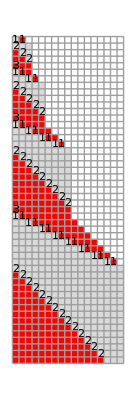
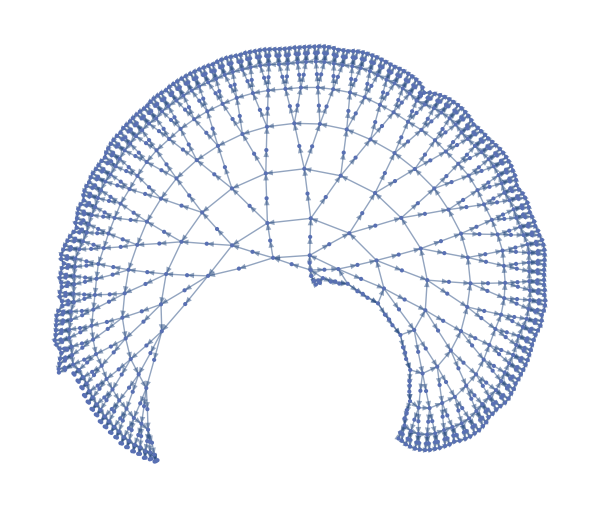
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs[["RuleSet"]], "AB",1000, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->50,NetMax->1000,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod-> Number,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

{1→2,1→3,1→4,2→5,5→6,3→6,6→7,4→7,6→8,6→9,«1452»,995→996,739→996,996→997,740→997,997→998,741→998,998→999,742→999,999→1000,743→1000}

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

{{1,2,3},{3},{3},{3},{1},{1,2,3},{3,4,5},{5},{5},{5},{5},{5},{1},{1,4,5},{1,5,6},{1,6,7},{7,8,9},{9},{9},{9},{9},{9},{9},{9},{9},{9},{1},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{15,16,17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{1},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{31,32,33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{1},{1,32,33},{1,33,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{1,39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{63,64,65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{1},{1,64,65},{1,65,66},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{1,79,80},{1,80,81},{1,81,82},{1,82,83},{1,83,84},{1,84,85},{1,85,86},{1,86,87},{1,87,88},{1,88,89},{1,89,90},{1,90,91},{1,91,92},{1,92,93},{1,93,94},{1,94,95},{1,95,96},{1,96,97},{1,97,98},{1,98,99},{1,99,100},{1,100,101},{1,101,102},{1,102,103},{1,103,104},{1,104,105},{1,105,106},{1,106,107},{1,107,108},{1,108,109},{1,109,110},{1,110,111},{1,111,112},{1,112,113},{1,113,114},{1,114,115},{1,115,116},{1,116,117},{1,117,118},{1,118,119},{1,119,120},{1,120,121},{1,121,122},{1,122,123},{1,123,124},{1,124,125},{1,125,126},{1,126,127},{127,128,129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{1},{1,128,129},{1,129,130},{1,130,131},{1,131,132},{1,132,133},{1,133,134},{1,134,135},{1,135,136},{1,136,137},{1,137,138},{1,138,139},{1,139,140},{1,140,141},{1,141,142},{1,142,143},{1,143,144},{1,144,145},{1,145,146},{1,146,147},{1,147,148},{1,148,149},{1,149,150},{1,150,151},{1,151,152},{1,152,153},{1,153,154},{1,154,155},{1,155,156},{1,156,157},{1,157,158},{1,158,159},{1,159,160},{1,160,161},{1,161,162},{1,162,163},{1,163,164},{1,164,165},{1,165,166},{1,166,167},{1,167,168},{1,168,169},{1,169,170},{1,170,171},{1,171,172},{1,172,173},{1,173,174},{1,174,175},{1,175,176},{1,176,177},{1,177,178},{1,178,179},{1,179,180},{1,180,181},{1,181,182},{1,182,183},{1,183,184},{1,184,185},{1,185,186},{1,186,187},{1,187,188},{1,188,189},{1,189,190},{1,190,191},{1,191,192},{1,192,193},{1,193,194},{1,194,195},{1,195,196},{1,196,197},{1,197,198},{1,198,199},{1,199,200},{1,200,201},{1,201,202},{1,202,203},{1,203,204},{1,204,205},{1,205,206},{1,206,207},{1,207,208},{1,208,209},{1,209,210},{1,210,211},{1,211,212},{1,212,213},{1,213,214},{1,214,215},{1,215,216},{1,216,217},{1,217,218},{1,218,219},{1,219,220},{1,220,221},{1,221,222},{1,222,223},{1,223,224},{1,224,225},{1,225,226},{1,226,227},{1,227,228},{1,228,229},{1,229,230},{1,230,231},{1,231,232},{1,232,233},{1,233,234},{1,234,235},{1,235,236},{1,236,237},{1,237,238},{1,238,239},{1,239,240},{1,240,241},{1,241,242},{1,242,243},{1,243,244},{1,244,245},{1,245,246},{1,246,247},{1,247,248},{1,248,249},{1,249,250},{1,250,251},{1,251,252},{1,252,253},{1,253,254},{1,254,255},{255,256,257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,{257}]
```

{{524},{525},{526},{527},{528},{529},{530},{531},{532},{533},{534},{535},{536},{537},{538},{539},{540},{541},{542},{543},{544},{545},{546},{547},{548},{549},{550},{551},{552},{553},{554},{555},{556},{557},{558},{559},{560},{561},{562},{563},{564},{565},{566},{567},{568},{569},{570},{571},{572},{573},{574},{575},{576},{577},{578},{579},{580},{581},{582},{583},{584},{585},{586},{587},{588},{589},{590},{591},{592},{593},{594},{595},{596},{597},{598},{599},{600},{601},{602},{603},{604},{605},{606},{607},{608},{609},{610},{611},{612},{613},{614},{615},{616},{617},{618},{619},{620},{621},{622},{623},{624},{625},{626},{627},{628},{629},{630},{631},{632},{633},{634},{635},{636},{637},{638},{639},{640},{641},{642},{643},{644},{645},{646},{647},{648},{649},{650},{651},{652},{653},{654},{655},{656},{657},{658},{659},{660},{661},{662},{663},{664},{665},{666},{667},{668},{669},{670},{671},{672},{673},{674},{675},{676},{677},{678},{679},{680},{681},{682},{683},{684},{685},{686},{687},{688},{689},{690},{691},{692},{693},{694},{695},{696},{697},{698},{699},{700},{701},{702},{703},{704},{705},{706},{707},{708},{709},{710},{711},{712},{713},{714},{715},{716},{717},{718},{719},{720},{721},{722},{723},{724},{725},{726},{727},{728},{729},{730},{731},{732},{733},{734},{735},{736},{737},{738},{739},{740},{741},{742},{743}}

```mathematica
nds[[1;;743]]
```

{{1,2,3},{3},{3},{3},{1},{1,2,3},{3,4,5},{5},{5},{5},{5},{5},{1},{1,4,5},{1,5,6},{1,6,7},{7,8,9},{9},{9},{9},{9},{9},{9},{9},{9},{9},{1},{1,8,9},{1,9,10},{1,10,11},{1,11,12},{1,12,13},{1,13,14},{1,14,15},{15,16,17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{17},{1},{1,16,17},{1,17,18},{1,18,19},{1,19,20},{1,20,21},{1,21,22},{1,22,23},{1,23,24},{1,24,25},{1,25,26},{1,26,27},{1,27,28},{1,28,29},{1,29,30},{1,30,31},{31,32,33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{33},{1},{1,32,33},{1,33,34},{1,34,35},{1,35,36},{1,36,37},{1,37,38},{1,38,39},{1,39,40},{1,40,41},{1,41,42},{1,42,43},{1,43,44},{1,44,45},{1,45,46},{1,46,47},{1,47,48},{1,48,49},{1,49,50},{1,50,51},{1,51,52},{1,52,53},{1,53,54},{1,54,55},{1,55,56},{1,56,57},{1,57,58},{1,58,59},{1,59,60},{1,60,61},{1,61,62},{1,62,63},{63,64,65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{65},{1},{1,64,65},{1,65,66},{1,66,67},{1,67,68},{1,68,69},{1,69,70},{1,70,71},{1,71,72},{1,72,73},{1,73,74},{1,74,75},{1,75,76},{1,76,77},{1,77,78},{1,78,79},{1,79,80},{1,80,81},{1,81,82},{1,82,83},{1,83,84},{1,84,85},{1,85,86},{1,86,87},{1,87,88},{1,88,89},{1,89,90},{1,90,91},{1,91,92},{1,92,93},{1,93,94},{1,94,95},{1,95,96},{1,96,97},{1,97,98},{1,98,99},{1,99,100},{1,100,101},{1,101,102},{1,102,103},{1,103,104},{1,104,105},{1,105,106},{1,106,107},{1,107,108},{1,108,109},{1,109,110},{1,110,111},{1,111,112},{1,112,113},{1,113,114},{1,114,115},{1,115,116},{1,116,117},{1,117,118},{1,118,119},{1,119,120},{1,120,121},{1,121,122},{1,122,123},{1,123,124},{1,124,125},{1,125,126},{1,126,127},{127,128,129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{129},{1},{1,128,129},{1,129,130},{1,130,131},{1,131,132},{1,132,133},{1,133,134},{1,134,135},{1,135,136},{1,136,137},{1,137,138},{1,138,139},{1,139,140},{1,140,141},{1,141,142},{1,142,143},{1,143,144},{1,144,145},{1,145,146},{1,146,147},{1,147,148},{1,148,149},{1,149,150},{1,150,151},{1,151,152},{1,152,153},{1,153,154},{1,154,155},{1,155,156},{1,156,157},{1,157,158},{1,158,159},{1,159,160},{1,160,161},{1,161,162},{1,162,163},{1,163,164},{1,164,165},{1,165,166},{1,166,167},{1,167,168},{1,168,169},{1,169,170},{1,170,171},{1,171,172},{1,172,173},{1,173,174},{1,174,175},{1,175,176},{1,176,177},{1,177,178},{1,178,179},{1,179,180},{1,180,181},{1,181,182},{1,182,183},{1,183,184},{1,184,185},{1,185,186},{1,186,187},{1,187,188},{1,188,189},{1,189,190},{1,190,191},{1,191,192},{1,192,193},{1,193,194},{1,194,195},{1,195,196},{1,196,197},{1,197,198},{1,198,199},{1,199,200},{1,200,201},{1,201,202},{1,202,203},{1,203,204},{1,204,205},{1,205,206},{1,206,207},{1,207,208},{1,208,209},{1,209,210},{1,210,211},{1,211,212},{1,212,213},{1,213,214},{1,214,215},{1,215,216},{1,216,217},{1,217,218},{1,218,219},{1,219,220},{1,220,221},{1,221,222},{1,222,223},{1,223,224},{1,224,225},{1,225,226},{1,226,227},{1,227,228},{1,228,229},{1,229,230},{1,230,231},{1,231,232},{1,232,233},{1,233,234},{1,234,235},{1,235,236},{1,236,237},{1,237,238},{1,238,239},{1,239,240},{1,240,241},{1,241,242},{1,242,243},{1,243,244},{1,244,245},{1,245,246},{1,246,247},{1,247,248},{1,248,249},{1,249,250},{1,250,251},{1,251,252},{1,252,253},{1,253,254},{1,254,255},{255,256,257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257},{257}}

Try the reduction:

```mathematica
rsl=ReduceSetList[nds[[1;;743]]]/. {n$2 -> k, n$1 -> j}
```

{€_(k⊨1)^7[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]],{255,256,257},€^220[{257}]}

```mathematica
rsl[[1;;1]]
```

{€_(k⊨1)^7[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]}

```mathematica
InputForm[rsl[[1 ;; 1]]]//InputForm
```

```mathematica
InputForm[{IndexedConcatenate[{-1 + 2^k, 2^k, 1 + 2^k}, IndexedConcatenate[{1 + 2^k}, 1 + 2^k], {1}, 
   IndexedConcatenate[{1, -1 + 2^k + j, 2^k + j}, {j, 1, -1 + 2^k}], {k, 1, 20}]}]
```

```mathematica
IndexedConcatenate[{-1 + 2^k, 2^k, 1 + 2^k}, IndexedConcatenate[{1 + 2^k}, 1 + 2^k], {1}, 
  IndexedConcatenate[{1, -1 + 2^k + j, 2^k + j}, {j, 1, -1 + 2^k}], {k, 1, 12}]
```

€_(k⊨1)^12[{-1+2^k,2^k,1+2^k},€^(1+2^k)[{1+2^k}],{1},€_(j⊨1)^(-1+2^k)[{1,-1+2^k+j,2^k+j}]]

The most compressed part is

```mathematica
{ExpandAll[%173]}
```

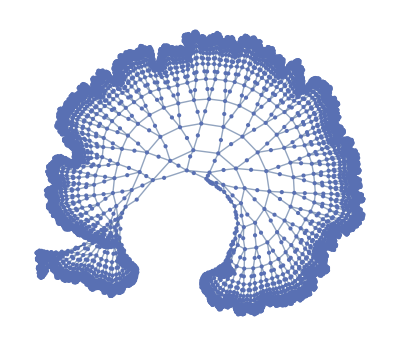

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```

```mathematica
GraphPlot3D[FromNetDifferenceSets@%161]
```

-Graphics3D-